# Practical 2 (b) Rahul Chopra | BSc(H) Computer Science | Sem - IV | 20211449 Regula Falsi Method

## Question 1 :

x0=1

x1=2

Nmax=10

epsilon=0.0001

f[x]:=Cos[x]

1th iteration value is:1.564904375891578

In 1th number of iterations the root is:1.5708

Estimated error is:1.

2th iteration value is:1.57097857453502

In 2th number of iterations the root is:1.5708

Estimated error is:0.435095624108422

3th iteration value is:1.57079632577305

In 3th number of iterations the root is:1.5708

Estimated error is:0.00607419864344

Return[1.5707963267949]

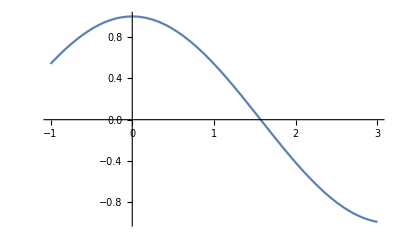

```mathematica
x0=Input["Enter first guess:"];
x1=Input["Enter second guess:"];
Nmax=Input["Enter maximum number of iterations:"];
eps=Input["Enter the value of convergence parameter:"];
Print["x0=",x0];
Print["x1=",x1];
Print["Nmax=",Nmax];
Print["epsilon=",eps];
f[x_]:=Cos[x];
Print["f[x]:=",f[x]];If[N[f[x0]*f[x1]]>0,
Print["These values do not satisfy the IVP so change the values."],
For[i=1,i≤Nmax,i++,a=N[x1-f[x1]*(x1-x0)/(f[x1]-f[x0]),16];
If[Abs[(x1-x0)/2]<eps,Return[N[a,16]],Print[i,"th iteration value is:",N[a,16]];
Print["In ",i,"th number of iterations the root is:",x2];
Print["Estimated error is:",N[x1-x0,16]];
If[f[a]*f[x1]>0,x1=a,x0=a]]];
Print["Root is:",N[a,16]];
Print["Estimated error is:",N[x1-x0,16]]];
Plot[f[x],{x,-1,3}]
```

## Question 2 :

x0=0

x1=1

Nmax=10

epsilon=0.0001

f[x]:=1-5 x+x^3

1th iteration value is:0.25

In 1th number of iterations the root is:0.517757

Estimated error is:1.

2th iteration value is:0.20253164556962

In 2th number of iterations the root is:0.517757

Estimated error is:0.25

3th iteration value is:0.201654334550389

In 3th number of iterations the root is:0.517757

Estimated error is:0.20253164556962

4th iteration value is:0.20163991608966

In 4th number of iterations the root is:0.517757

Estimated error is:0.201654334550389

5th iteration value is:0.20163967966463

In 5th number of iterations the root is:0.517757

Estimated error is:0.20163991608966

6th iteration value is:0.20163967578803

In 6th number of iterations the root is:0.517757

Estimated error is:0.20163967966463

7th iteration value is:0.2016396757245

In 7th number of iterations the root is:0.517757

Estimated error is:0.20163967578803

8th iteration value is:0.2016396757234

In 8th number of iterations the root is:0.517757

Estimated error is:0.2016396757245

9th iteration value is:0.2016396757234

In 9th number of iterations the root is:0.517757

Estimated error is:0.2016396757234

Return[0.201639675723]

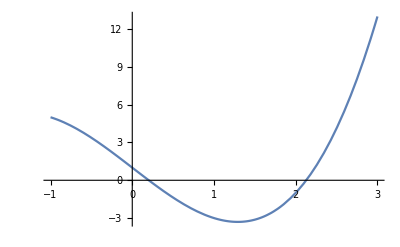

```mathematica
x0=Input["Enter first guess:"];
x1=Input["Enter second guess:"];
Nmax=Input["Enter maximum number of iterations:"];
eps=Input["Enter the value of convergence parameter:"];
Print["x0=",x0];
Print["x1=",x1];
Print["Nmax=",Nmax];
Print["epsilon=",eps];
f[x_]:=x^3-5x+1;
Print["f[x]:=",f[x]];If[N[f[x0]*f[x1]]>0,
Print["These values do not satisfy the IVP so change the values."],
For[i=1,i≤Nmax,i++,a=N[x1-f[x1]*(x1-x0)/(f[x1]-f[x0]),16];
If[Abs[(x1-x0)/2]<eps,Return[N[a,16]],Print[i,"th iteration value is:",N[a,16]];
Print["In ",i,"th number of iterations the root is:",x2];
Print["Estimated error is:",N[x1-x0,16]];
If[f[a]*f[x1]>0,x1=a,x0=a]]];
Print["Root is:",N[a,16]];
Print["Estimated error is:",N[x1-x0,16]]];
Plot[f[x],{x,-1,3}]
```

## Question 3 :

x0=0

x1=1

Nmax=10

epsilon=0.0001

f[x]:=-ⅇ^x x+Cos[x]

1th iteration value is:0.3146653378007709

In 1th number of iterations the root is:0.517757

Estimated error is:1.

2th iteration value is:0.4467281445913339

In 2th number of iterations the root is:0.517757

Estimated error is:0.6853346621992291

3th iteration value is:0.494015336595899

In 3th number of iterations the root is:0.517757

Estimated error is:0.5532718554086661

4th iteration value is:0.509946140365247

In 4th number of iterations the root is:0.517757

Estimated error is:0.505984663404101

5th iteration value is:0.51520100990225

In 5th number of iterations the root is:0.517757

Estimated error is:0.490053859634753

6th iteration value is:0.516922210010517

In 6th number of iterations the root is:0.517757

Estimated error is:0.48479899009775

7th iteration value is:0.517484676784512

In 7th number of iterations the root is:0.517757

Estimated error is:0.483077789989483

8th iteration value is:0.51766834497773

In 8th number of iterations the root is:0.517757

Estimated error is:0.48251532321549

9th iteration value is:0.51772830527141

In 9th number of iterations the root is:0.517757

Estimated error is:0.48233165502227

10th iteration value is:0.51774787832211

In 10th number of iterations the root is:0.517757

Estimated error is:0.48227169472859

Root is:0.51774787832211

Estimated error is:0.48225212167789

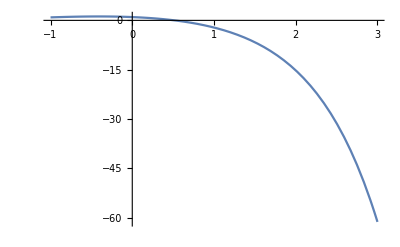

```mathematica
x0=Input["Enter first guess:"];
x1=Input["Enter second guess:"];
Nmax=Input["Enter maximum number of iterations:"];
eps=Input["Enter the value of convergence parameter:"];
Print["x0=",x0];
Print["x1=",x1];
Print["Nmax=",Nmax];
Print["epsilon=",eps];
f[x_]:=Cos[x]-x*Exp[x];
Print["f[x]:=",f[x]];If[N[f[x0]*f[x1]]>0,
Print["These values do not satisfy the IVP so change the values."],
For[i=1,i≤Nmax,i++,a=N[x1-f[x1]*(x1-x0)/(f[x1]-f[x0]),16];
If[Abs[(x1-x0)/2]<eps,Return[N[a,16]],Print[i,"th iteration value is:",N[a,16]];
Print["In ",i,"th number of iterations the root is:",x2];
Print["Estimated error is:",N[x1-x0,16]];
If[f[a]*f[x1]>0,x1=a,x0=a]]];
Print["Root is:",N[a,16]];
Print["Estimated error is:",N[x1-x0,16]]];
Plot[f[x],{x,-1,3}]
```